# Choi purity vs reduced-state purity

## Definitions and packages

```mathematica
Needs["QMB`"]
```

```mathematica
Import["/home/jadeleon/Documents/chaos_meets_channels/Mathematica_packages/Chaometer.wl"]
```

```mathematica
?Chaometer`*
```

E_ψ=1/6(𝒰+4 𝒫)

## L=3

```mathematica
L=3;(*number of spins*)
```

```mathematica
(*environment's initial state*)
ψ=RandomChainProductState[L-1];
```

## h_x=J=1, h_z=0.5 (chaotic)

```mathematica
(*parameters*) 
hx=1.;(*transverse field*)
hz=0.5;(*longitudinal field*)
J=1.;(*ising interaction*)
```

```mathematica
H=IsingHamiltonian[hx,hz,J,L];
{energies,eigenstates}=Eigensystem[Normal[H]];
```

```mathematica
state2design=Catenate[Eigenvectors[N@Pauli[#]]&/@Range[3]]
```

{{-0.707107,0.707107},{0.707107,0.707107},{0.-0.707107 ⅈ,-0.707107+0. ⅈ},{0.-0.707107 ⅈ,0.707107+0. ⅈ},{0.,-1.},{-1.,0.}}

```mathematica
purities=Table[
ℰ=Superoperator[t,ψ,energies,eigenstates,L];
{Purity[Reshuffle[ℰ]/2],Mean[Braket[#,#]&[ℰ.Flatten[Dyad[#]]]&/@state2design]}
,{t,0,10,0.1}];
```

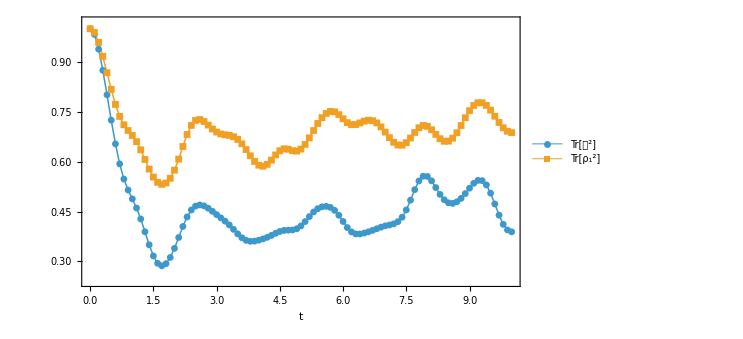

```mathematica
ListPlot[Transpose[{Range[0,10,0.1],#}]&/@Transpose[purities],
PlotRange->{All,{0.24,1.02}},
Joined->True,
PlotMarkers->{Automatic,7},
PlotStyle->Directive[Thickness[0.002]],
PlotLegends->Placed[LineLegend[{TraditionalForm[Tr[𝒟^2]],TraditionalForm[Tr[Subscript[ρ, 1]^2]]},LabelStyle->Directive[Black,FontSize->22]], {Right,Top}],
Frame->True,
FrameStyle->Directive[Black,FontSize->25],
FrameLabel->{"t",""},
ImageSize->550
]
```

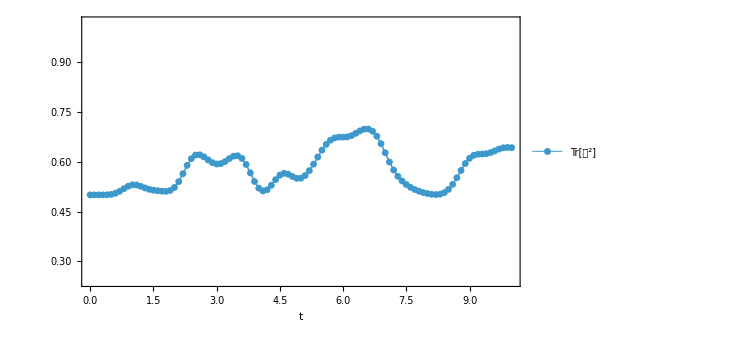

```mathematica
ListPlot[Transpose[{Range[0,10,0.1],3/2*#2-#1&@@Transpose[purities]}],
PlotRange->{All,{0.24,1.02}},
Joined->True,
PlotMarkers->{Automatic,7},
PlotStyle->Directive[Thickness[0.002]],
PlotLegends->Placed[LineLegend[{TraditionalForm[Tr[𝒟^2]],TraditionalForm[Tr[Subscript[ρ, 1]^2]]},LabelStyle->Directive[Black,FontSize->22]], {Right,Top}],
Frame->True,
FrameStyle->Directive[Black,FontSize->25],
FrameLabel->{"t",""},
ImageSize->550
]
```

## h_x=J=1, h_z=2.5 (integrable)

```mathematica
(*parameters*) 

hx=1.;(*transverse field*)
hz=0.001;(*longitudinal field*)
J=1.;(*ising interaction*)
```

```mathematica
H=IsingHamiltonian[hx,hz,J,L];
{energies,eigenstates}=Eigensystem[Normal[H]];
```

```mathematica
state2design=Catenate[Eigenvectors[N@Pauli[#]]&/@Range[3]]
```

{{-0.707107,0.707107},{0.707107,0.707107},{0.-0.707107 ⅈ,-0.707107+0. ⅈ},{0.-0.707107 ⅈ,0.707107+0. ⅈ},{0.,-1.},{-1.,0.}}

```mathematica
purities=Table[
ℰ=Superoperator[t,ψ,energies,eigenstates,L];
{Purity[Reshuffle[ℰ]/2],Mean[Braket[#,#]&[ℰ.Flatten[Dyad[#]]]&/@state2design]}
,{t,0,10,0.1}];
```

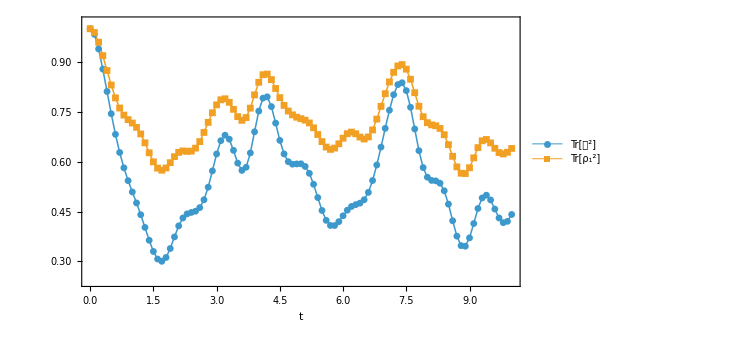

```mathematica
ListPlot[Transpose[{Range[0,10,0.1],#}]&/@Transpose[purities],
PlotRange->{All,{0.24,1.02}},
Joined->True,
PlotMarkers->{Automatic,7},
PlotStyle->Directive[Thickness[0.002]],
PlotLegends->Placed[LineLegend[{TraditionalForm[Tr[𝒟^2]],TraditionalForm[Tr[Subscript[ρ, 1]^2]]},LabelStyle->Directive[Black,FontSize->22]], {Right,Top}],
Frame->True,
FrameStyle->Directive[Black,FontSize->25],
FrameLabel->{"t",""},
ImageSize->550
]
```

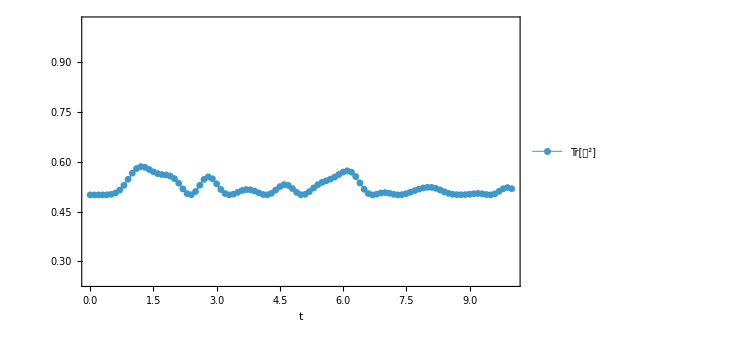

```mathematica
ListPlot[Transpose[{Range[0,10,0.1],3/2*#2-#1&@@Transpose[purities]}],
PlotRange->{All,{0.24,1.02}},
Joined->True,
PlotMarkers->{Automatic,7},
PlotStyle->Directive[Thickness[0.002]],
PlotLegends->Placed[LineLegend[{TraditionalForm[Tr[𝒟^2]],TraditionalForm[Tr[Subscript[ρ, 1]^2]]},LabelStyle->Directive[Black,FontSize->22]], {Right,Top}],
Frame->True,
FrameStyle->Directive[Black,FontSize->25],
FrameLabel->{"t",""},
ImageSize->550
]
```

## L=4

```mathematica
L=4;(*number of spins*)
```

```mathematica
(*environment's initial state*)
ψ=RandomChainProductState[L-1];
```

## h_x=J=1, h_z=0.5 (chaotic)

```mathematica
(*parameters*) 
hx=1.;(*transverse field*)
hz=0.5;(*longitudinal field*)
J=1.;(*ising interaction*)
```

```mathematica
H=IsingHamiltonian[hx,hz,J,L];
{energies,eigenstates}=Eigensystem[Normal[H]];
```

```mathematica
state2design=Catenate[Eigenvectors[N@Pauli[#]]&/@Range[3]]
```

{{-0.707107,0.707107},{0.707107,0.707107},{0.-0.707107 ⅈ,-0.707107+0. ⅈ},{0.-0.707107 ⅈ,0.707107+0. ⅈ},{0.,-1.},{-1.,0.}}

```mathematica
purities=Table[
ℰ=Superoperator[t,ψ,energies,eigenstates,L];
{Purity[Reshuffle[ℰ]/2],Mean[Braket[#,#]&[ℰ.Flatten[Dyad[#]]]&/@state2design]}
,{t,0,10,0.1}];
```

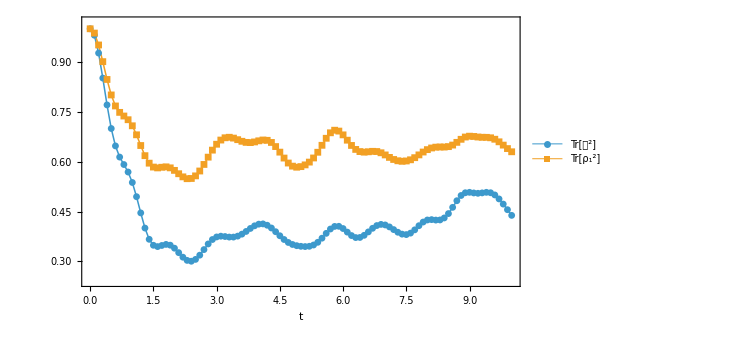

```mathematica
ListPlot[Transpose[{Range[0,10,0.1],#}]&/@Transpose[purities],
PlotRange->{All,{0.24,1.02}},
Joined->True,
PlotMarkers->{Automatic,7},
PlotStyle->Directive[Thickness[0.002]],
PlotLegends->Placed[LineLegend[{TraditionalForm[Tr[𝒟^2]],TraditionalForm[Tr[Subscript[ρ, 1]^2]]},LabelStyle->Directive[Black,FontSize->22]], {Right,Top}],
Frame->True,
FrameStyle->Directive[Black,FontSize->25],
FrameLabel->{"t",""},
ImageSize->550
]
```

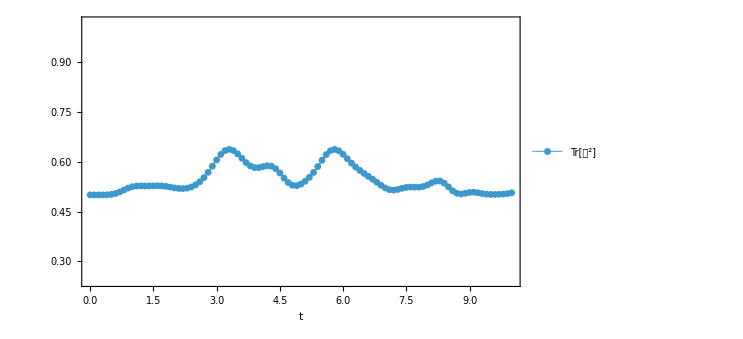

```mathematica
ListPlot[Transpose[{Range[0,10,0.1],3/2*#2-#1&@@Transpose[purities]}],
PlotRange->{All,{0.24,1.02}},
Joined->True,
PlotMarkers->{Automatic,7},
PlotStyle->Directive[Thickness[0.002]],
PlotLegends->Placed[LineLegend[{TraditionalForm[Tr[𝒟^2]],TraditionalForm[Tr[Subscript[ρ, 1]^2]]},LabelStyle->Directive[Black,FontSize->22]], {Right,Top}],
Frame->True,
FrameStyle->Directive[Black,FontSize->25],
FrameLabel->{"t",""},
ImageSize->550
]
```

## h_x=J=1, h_z=2.5 (integrable)

```mathematica
(*parameters*) 

hx=1.;(*transverse field*)
hz=0.001;(*longitudinal field*)
J=1.;(*ising interaction*)
```

```mathematica
H=IsingHamiltonian[hx,hz,J,L];
{energies,eigenstates}=Eigensystem[Normal[H]];
```

```mathematica
state2design=Catenate[Eigenvectors[N@Pauli[#]]&/@Range[3]]
```

{{-0.707107,0.707107},{0.707107,0.707107},{0.-0.707107 ⅈ,-0.707107+0. ⅈ},{0.-0.707107 ⅈ,0.707107+0. ⅈ},{0.,-1.},{-1.,0.}}

```mathematica
purities=Table[
ℰ=Superoperator[t,ψ,energies,eigenstates,L];
{Purity[Reshuffle[ℰ]/2],Mean[Braket[#,#]&[ℰ.Flatten[Dyad[#]]]&/@state2design]}
,{t,0,10,0.1}];
```

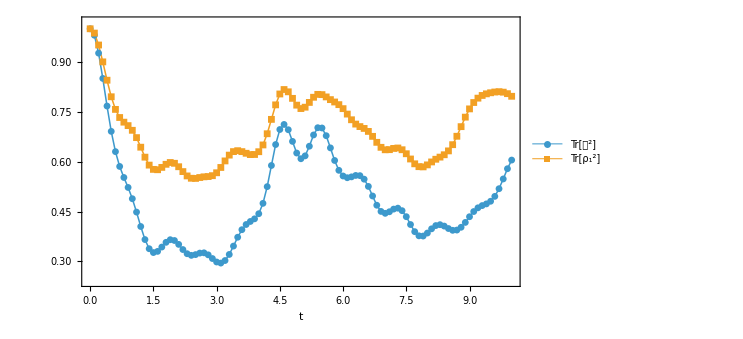

```mathematica
ListPlot[Transpose[{Range[0,10,0.1],#}]&/@Transpose[purities],
PlotRange->{All,{0.24,1.02}},
Joined->True,
PlotMarkers->{Automatic,7},
PlotStyle->Directive[Thickness[0.002]],
PlotLegends->Placed[LineLegend[{TraditionalForm[Tr[𝒟^2]],TraditionalForm[Tr[Subscript[ρ, 1]^2]]},LabelStyle->Directive[Black,FontSize->22]], {Right,Top}],
Frame->True,
FrameStyle->Directive[Black,FontSize->25],
FrameLabel->{"t",""},
ImageSize->550
]
```

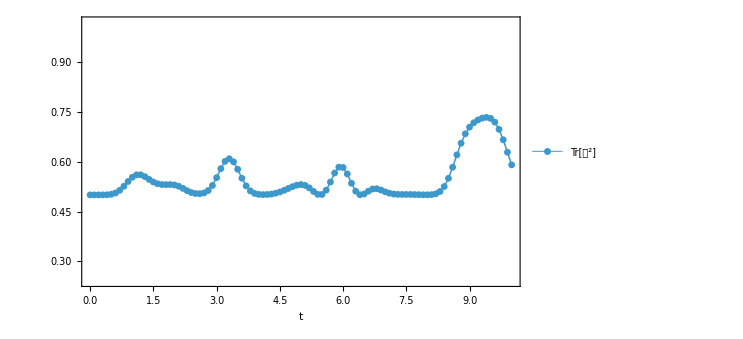

```mathematica
ListPlot[Transpose[{Range[0,10,0.1],3/2*#2-#1&@@Transpose[purities]}],
PlotRange->{All,{0.24,1.02}},
Joined->True,
PlotMarkers->{Automatic,7},
PlotStyle->Directive[Thickness[0.002]],
PlotLegends->Placed[LineLegend[{TraditionalForm[Tr[𝒟^2]],TraditionalForm[Tr[Subscript[ρ, 1]^2]]},LabelStyle->Directive[Black,FontSize->22]], {Right,Top}],
Frame->True,
FrameStyle->Directive[Black,FontSize->25],
FrameLabel->{"t",""},
ImageSize->550
]
```

## L=5

```mathematica
L=5;(*number of spins*)
```

```mathematica
(*environment's initial state*)
ψ=RandomChainProductState[L-1];
```

## h_x=J=1, h_z=0.5 (chaotic)

```mathematica
(*parameters*) 
hx=1.;(*transverse field*)
hz=0.5;(*longitudinal field*)
J=1.;(*ising interaction*)
```

```mathematica
H=IsingHamiltonian[hx,hz,J,L];
{energies,eigenstates}=Eigensystem[Normal[H]];
```

```mathematica
state2design=Catenate[Eigenvectors[N@Pauli[#]]&/@Range[3]]
```

{{-0.707107,0.707107},{0.707107,0.707107},{0.-0.707107 ⅈ,-0.707107+0. ⅈ},{0.-0.707107 ⅈ,0.707107+0. ⅈ},{0.,-1.},{-1.,0.}}

```mathematica
purities=Table[
ℰ=Superoperator[t,ψ,energies,eigenstates,L];
{Purity[Reshuffle[ℰ]/2],Mean[Braket[#,#]&[ℰ.Flatten[Dyad[#]]]&/@state2design]}
,{t,0,10,0.1}];
```

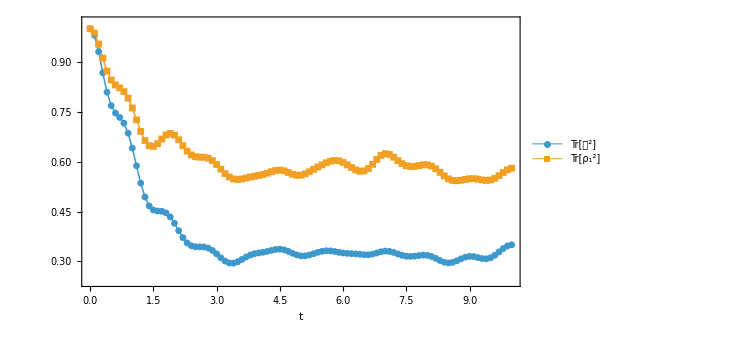

```mathematica
ListPlot[Transpose[{Range[0,10,0.1],#}]&/@Transpose[purities],
PlotRange->{All,{0.24,1.02}},
Joined->True,
PlotMarkers->{Automatic,7},
PlotStyle->Directive[Thickness[0.002]],
PlotLegends->Placed[LineLegend[{TraditionalForm[Tr[𝒟^2]],TraditionalForm[Tr[Subscript[ρ, 1]^2]]},LabelStyle->Directive[Black,FontSize->22]], {Right,Top}],
Frame->True,
FrameStyle->Directive[Black,FontSize->25],
FrameLabel->{"t",""},
ImageSize->550
]
```

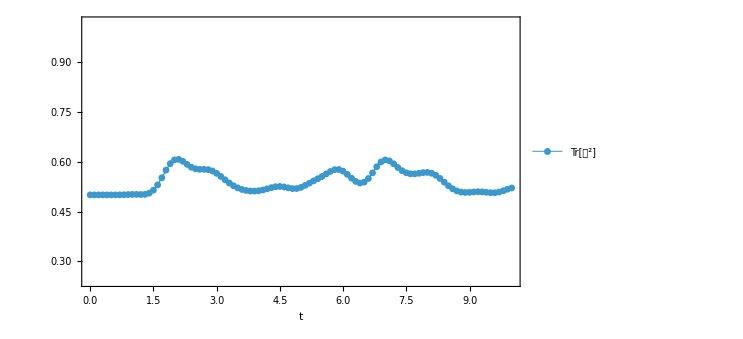

```mathematica
ListPlot[Transpose[{Range[0,10,0.1],3/2*#2-#1&@@Transpose[purities]}],
PlotRange->{All,{0.24,1.02}},
Joined->True,
PlotMarkers->{Automatic,7},
PlotStyle->Directive[Thickness[0.002]],
PlotLegends->Placed[LineLegend[{TraditionalForm[Tr[𝒟^2]],TraditionalForm[Tr[Subscript[ρ, 1]^2]]},LabelStyle->Directive[Black,FontSize->22]], {Right,Top}],
Frame->True,
FrameStyle->Directive[Black,FontSize->25],
FrameLabel->{"t",""},
ImageSize->550
]
```

## h_x=J=1, h_z=2.5 (integrable)

```mathematica
tf=100.;
```

```mathematica
(*environment's initial state*)
ψ=RandomChainProductState[L-1];
```

```mathematica
(*parameters*) 

hx=1.;(*transverse field*)
hz=0.5;(*longitudinal field*)
J=3.;(*ising interaction*)
```

```mathematica
H=IsingHamiltonian[hx,hz,J,L];
{energies,eigenstates}=Eigensystem[Normal[H]];
```

```mathematica
state2design=Catenate[Eigenvectors[N@Pauli[#]]&/@Range[3]]
```

{{-0.707107,0.707107},{0.707107,0.707107},{0.-0.707107 ⅈ,-0.707107+0. ⅈ},{0.-0.707107 ⅈ,0.707107+0. ⅈ},{0.,-1.},{-1.,0.}}

```mathematica
purities=Table[
ℰ=Superoperator[t,ψ,energies,eigenstates,L];
{Purity[Reshuffle[ℰ]/2],Mean[Braket[#,#]&[ℰ.Flatten[Dyad[#]]]&/@state2design]}
,{t,0,tf,0.1}];
```

```mathematica
fig1=ListPlot[Transpose[{Range[0,tf,0.1],#}]&/@Transpose[purities],
PlotRange->{All,{0.24,1.02}},
Joined->True,
PlotMarkers->{Automatic,7},
PlotStyle->Directive[Thickness[0.002]],
PlotLegends->Placed[LineLegend[{TraditionalForm[Tr[𝒟^2]],TraditionalForm[Tr[Subscript[ρ, 1]^2]]},LabelStyle->Directive[Black,FontSize->22]], {Right,Top}],
Frame->True,
FrameStyle->Directive[Black,FontSize->25],
FrameLabel->{"t",""},
ImageSize->550
];
```

```mathematica
fig2=ListPlot[Transpose[{Range[0,tf,0.1],3/2*#2-#1&@@Transpose[purities]}],
PlotRange->{All,{0.49,0.65}},
Joined->True,
PlotMarkers->{Automatic,7},
PlotStyle->Directive[Thickness[0.002]],
PlotLegends->Placed[LineLegend[{TraditionalForm[Tr[𝒟^2]],TraditionalForm[Tr[Subscript[ρ, 1]^2]]},LabelStyle->Directive[Black,FontSize->22]], {Right,Top}],
Frame->True,
FrameStyle->Directive[Black,FontSize->25],
FrameLabel->{"t",""},
ImageSize->550
];
```

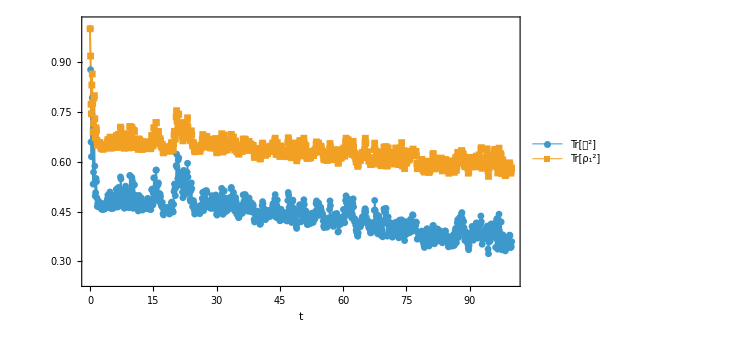
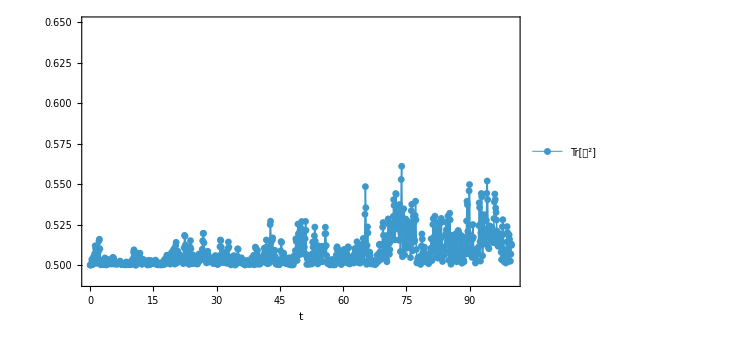

```mathematica
{fig1,fig2}
```

## h_x=J=1, h_z=2.5 (integrable)

```mathematica
tf=100.;
```

```mathematica
(*environment's initial state*)
ψ=RandomChainProductState[L-1];
```

```mathematica
(*parameters*) 

hx=1.;(*transverse field*)
hz=2.5;(*longitudinal field*)
J=0.5;(*ising interaction*)
```

```mathematica
H=IsingHamiltonian[hx,hz,J,L];
{energies,eigenstates}=Eigensystem[Normal[H]];
```

```mathematica
state2design=Catenate[Eigenvectors[N@Pauli[#]]&/@Range[3]]
```

{{-0.707107,0.707107},{0.707107,0.707107},{0.-0.707107 ⅈ,-0.707107+0. ⅈ},{0.-0.707107 ⅈ,0.707107+0. ⅈ},{0.,-1.},{-1.,0.}}

```mathematica
purities=Table[
ℰ=Superoperator[t,ψ,energies,eigenstates,L];
{Purity[Reshuffle[ℰ]/2],Mean[Braket[#,#]&[ℰ.Flatten[Dyad[#]]]&/@state2design]}
,{t,0,tf,0.1}];
```

```mathematica
fig1=ListPlot[Transpose[{Range[0,tf,0.1],#}]&/@Transpose[purities],
PlotRange->{All,{0.24,1.02}},
Joined->True,
PlotMarkers->{Automatic,7},
PlotStyle->Directive[Thickness[0.002]],
PlotLegends->Placed[LineLegend[{TraditionalForm[Tr[𝒟^2]],TraditionalForm[Tr[Subscript[ρ, 1]^2]]},LabelStyle->Directive[Black,FontSize->22]], {Right,Top}],
Frame->True,
FrameStyle->Directive[Black,FontSize->25],
FrameLabel->{"t",""},
ImageSize->550
];
```

```mathematica
fig2=ListPlot[Transpose[{Range[0,tf,0.1],3/2*#2-#1&@@Transpose[purities]}],
PlotRange->{All,{0.49,0.65}},
Joined->True,
PlotMarkers->{Automatic,7},
PlotStyle->Directive[Thickness[0.002]],
PlotLegends->Placed[LineLegend[{TraditionalForm[Tr[𝒟^2]],TraditionalForm[Tr[Subscript[ρ, 1]^2]]},LabelStyle->Directive[Black,FontSize->22]], {Right,Top}],
Frame->True,
FrameStyle->Directive[Black,FontSize->25],
FrameLabel->{"t",""},
ImageSize->550
];
```

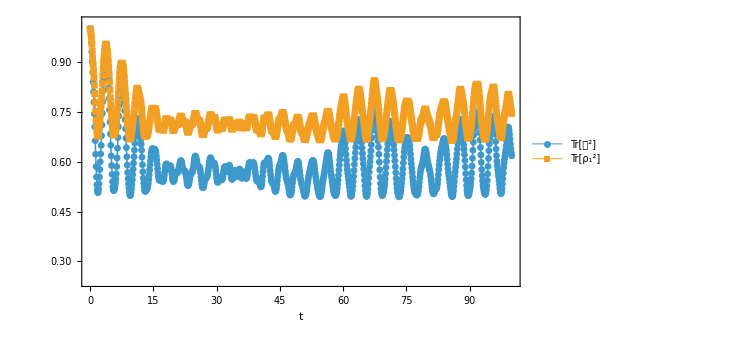
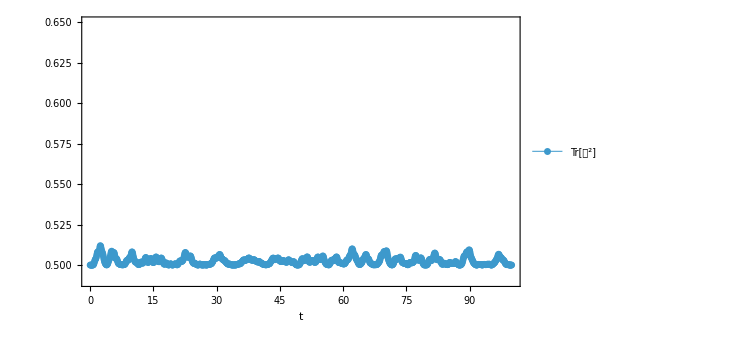

```mathematica
{fig1,fig2}
```

## h_x=J=1, h_z=2.5 (integrable)

```mathematica
tf=100.;
```

```mathematica
(*environment's initial state*)
ψ=RandomChainProductState[L-1];
```

```mathematica
(*parameters*) 

hx=1.;(*transverse field*)
hz=1.446;(*longitudinal field*)
J=0.05;(*ising interaction*)
```

```mathematica
H=IsingHamiltonian[hx,hz,J,L];
{energies,eigenstates}=Eigensystem[Normal[H]];
```

```mathematica
state2design=Catenate[Eigenvectors[N@Pauli[#]]&/@Range[3]]
```

{{-0.707107,0.707107},{0.707107,0.707107},{0.-0.707107 ⅈ,-0.707107+0. ⅈ},{0.-0.707107 ⅈ,0.707107+0. ⅈ},{0.,-1.},{-1.,0.}}

```mathematica
purities=Table[
ℰ=Superoperator[t,ψ,energies,eigenstates,L];
{Purity[Reshuffle[ℰ]/2],Mean[Braket[#,#]&[ℰ.Flatten[Dyad[#]]]&/@state2design]}
,{t,0,tf,0.1}];
```

```mathematica
fig1=ListPlot[Transpose[{Range[0,tf,0.1],#}]&/@Transpose[purities],
PlotRange->{All,{0.24,1.02}},
Joined->True,
PlotMarkers->{Automatic,7},
PlotStyle->Directive[Thickness[0.002]],
PlotLegends->Placed[LineLegend[{TraditionalForm[Tr[𝒟^2]],TraditionalForm[Tr[Subscript[ρ, 1]^2]]},LabelStyle->Directive[Black,FontSize->22]], {Right,Top}],
Frame->True,
FrameStyle->Directive[Black,FontSize->25],
FrameLabel->{"t",""},
ImageSize->550
];
```

```mathematica
fig2=ListPlot[Transpose[{Range[0,tf,0.1],3/2*#2-#1&@@Transpose[purities]}],
PlotRange->{All,{0.49,0.65}},
Joined->True,
PlotMarkers->{Automatic,7},
PlotStyle->Directive[Thickness[0.002]],
PlotLegends->Placed[LineLegend[{TraditionalForm[Tr[𝒟^2]],TraditionalForm[Tr[Subscript[ρ, 1]^2]]},LabelStyle->Directive[Black,FontSize->22]], {Right,Top}],
Frame->True,
FrameStyle->Directive[Black,FontSize->25],
FrameLabel->{"t",""},
ImageSize->550
];
```

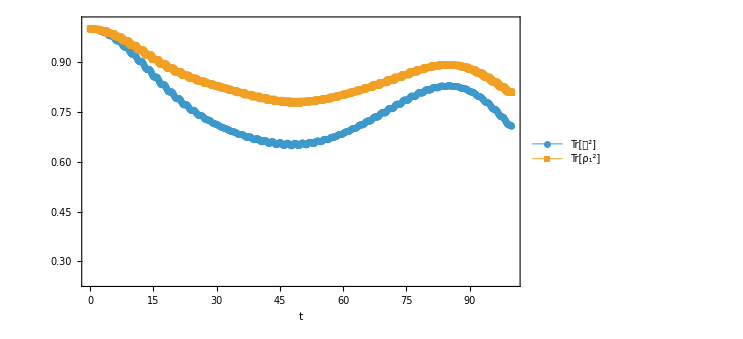
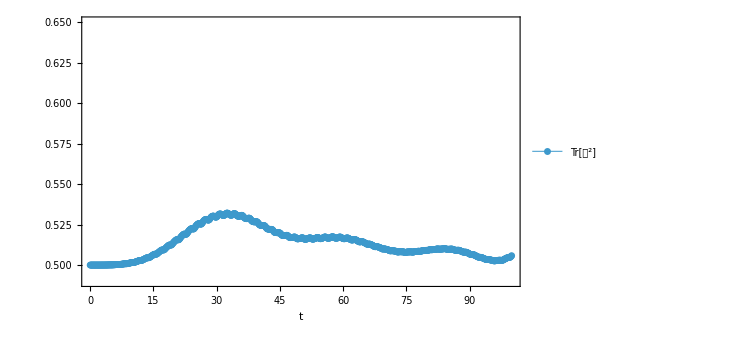

```mathematica
{fig1,fig2}
```

## (caotico)

```mathematica
L=3;
```

```mathematica
tf=100.;
```

```mathematica
(*environment's initial state*)
ψ=RandomChainProductState[L-1];
```

```mathematica
(*parameters*) 

hx=1.;(*transverse field*)
hz=0.48;(*longitudinal field*)
J=0.8;(*ising interaction*)
```

```mathematica
H=IsingHamiltonian[hx,hz,J,L];
{energies,eigenstates}=Eigensystem[Normal[H]];
```

```mathematica
state2design=Catenate[Eigenvectors[N@Pauli[#]]&/@Range[3]]
```

{{-0.707107,0.707107},{0.707107,0.707107},{0.-0.707107 ⅈ,-0.707107+0. ⅈ},{0.-0.707107 ⅈ,0.707107+0. ⅈ},{0.,-1.},{-1.,0.}}

```mathematica
purities=Table[
ℰ=Superoperator[t,ψ,energies,eigenstates,L];
{Purity[Reshuffle[ℰ]/2],Mean[Braket[#,#]&[ℰ.Flatten[Dyad[#]]]&/@state2design]}
,{t,0,tf,0.1}];
```

```mathematica
fig1=ListPlot[Transpose[{Range[0,tf,0.1],#}]&/@Transpose[purities],
PlotRange->{All,{0.24,1.02}},
Joined->True,
PlotMarkers->{Automatic,7},
PlotStyle->Directive[Thickness[0.002]],
PlotLegends->Placed[LineLegend[{TraditionalForm[Tr[𝒟^2]],TraditionalForm[Tr[Subscript[ρ, 1]^2]]},LabelStyle->Directive[Black,FontSize->22]], {Right,Top}],
Frame->True,
FrameStyle->Directive[Black,FontSize->25],
FrameLabel->{"t",""},
ImageSize->550
];
```

```mathematica
fig2=ListPlot[Transpose[{Range[0,tf,0.1],3/2*#2-#1&@@Transpose[purities]}],
PlotRange->{All,{0.49,0.65}},
Joined->True,
PlotMarkers->{Automatic,7},
PlotStyle->Directive[Thickness[0.002]],
PlotLegends->Placed[LineLegend[{TraditionalForm[Tr[𝒟^2]],TraditionalForm[Tr[Subscript[ρ, 1]^2]]},LabelStyle->Directive[Black,FontSize->22]], {Right,Top}],
Frame->True,
FrameStyle->Directive[Black,FontSize->25],
FrameLabel->{"t",""},
ImageSize->550
];
```

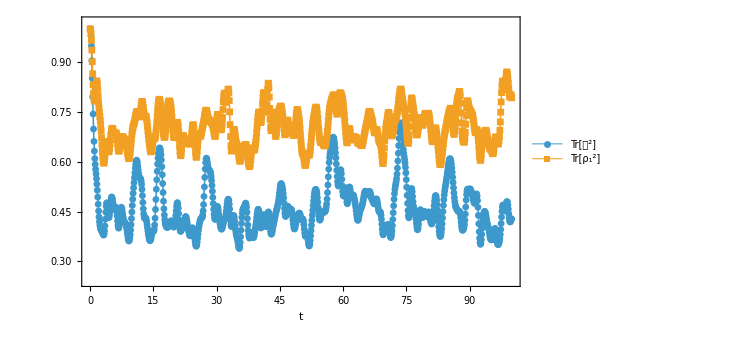
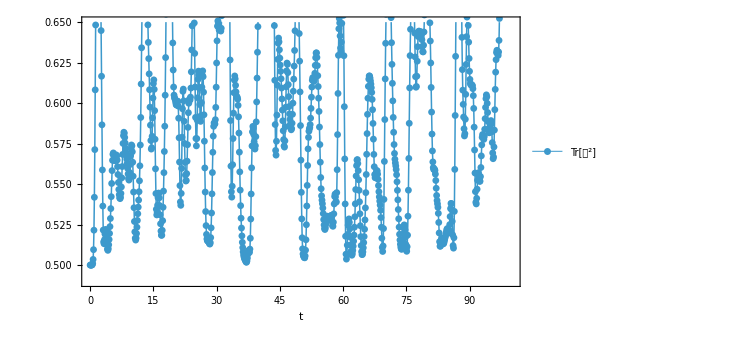

```mathematica
{fig1,fig2}
```

## (caotico) 1

```mathematica
L=3;
```

```mathematica
tf=1000.;
```

```mathematica
(*environment's initial state*)
ψ=RandomChainProductState[L-1];
```

```mathematica
(*parameters*) 

hx=1.;(*transverse field*)
hz=1.;(*longitudinal field*)
J=1.;(*ising interaction*)
```

```mathematica
H=IsingHamiltonian[hx,hz,J,L];
{energies,eigenstates}=Eigensystem[Normal[H]];
```

```mathematica
state2design=Catenate[Eigenvectors[N@Pauli[#]]&/@Range[3]]
```

{{-0.707107,0.707107},{0.707107,0.707107},{0.-0.707107 ⅈ,-0.707107+0. ⅈ},{0.-0.707107 ⅈ,0.707107+0. ⅈ},{0.,-1.},{-1.,0.}}

```mathematica
purities=Table[
ℰ=Superoperator[t,ψ,energies,eigenstates,L];
{Purity[Reshuffle[ℰ]/2],Mean[Braket[#,#]&[ℰ.Flatten[Dyad[#]]]&/@state2design]}
,{t,0,tf,0.1}];
```

```mathematica
fig1=ListPlot[Transpose[{Range[0,tf,0.1],#}]&/@Transpose[purities],
PlotRange->{All,{0.24,1.02}},
Joined->True,
PlotMarkers->{Automatic,7},
PlotStyle->Directive[Thickness[0.002]],
PlotLegends->Placed[LineLegend[{TraditionalForm[Tr[𝒟^2]],TraditionalForm[Tr[Subscript[ρ, 1]^2]]},LabelStyle->Directive[Black,FontSize->22]], {Right,Top}],
Frame->True,
FrameStyle->Directive[Black,FontSize->25],
FrameLabel->{"t",""},
ImageSize->550
];
```

```mathematica
fig2=ListPlot[Transpose[{Range[0,tf,0.1],3/2*#2-#1&@@Transpose[purities]}],
PlotRange->{All,All},
Joined->True,
PlotMarkers->{Automatic,7},
PlotStyle->Directive[Thickness[0.002]],
PlotLegends->Placed[LineLegend[{TraditionalForm[Tr[𝒟^2]],TraditionalForm[Tr[Subscript[ρ, 1]^2]]},LabelStyle->Directive[Black,FontSize->22]], {Right,Top}],
Frame->True,
FrameStyle->Directive[Black,FontSize->25],
FrameLabel->{"t",""},
ImageSize->550
];
```

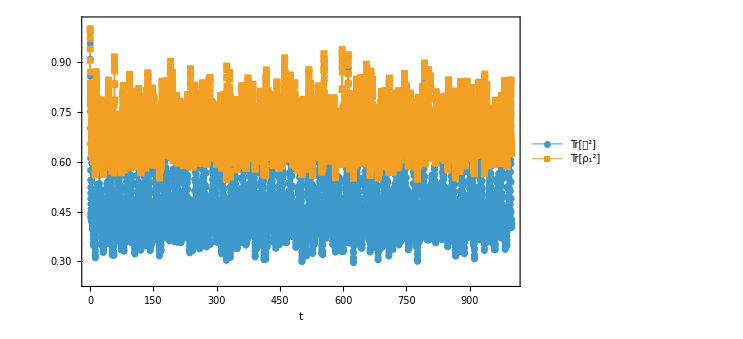
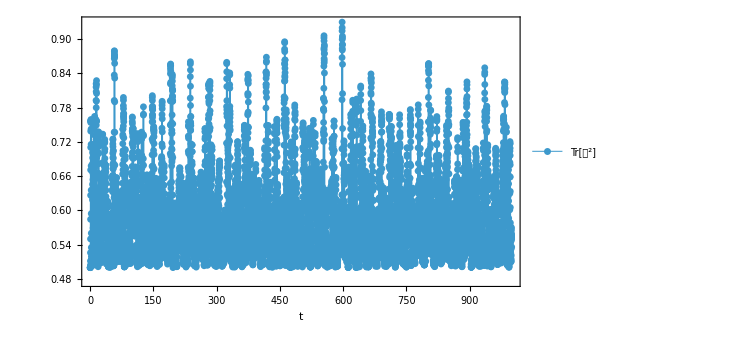

```mathematica
{fig1,fig2}
```

## (caotico) 0.5

```mathematica
L=3;
```

```mathematica
tf=1000.;
```

```mathematica
(*environment's initial state*)
ψ=RandomChainProductState[L-1];
```

```mathematica
(*parameters*) 

hx=1.;(*transverse field*)
hz=0.5;(*longitudinal field*)
J=1.;(*ising interaction*)
```

```mathematica
H=IsingHamiltonian[hx,hz,J,L];
{energies,eigenstates}=Eigensystem[Normal[H]];
```

```mathematica
state2design=Catenate[Eigenvectors[N@Pauli[#]]&/@Range[3]]
```

{{-0.707107,0.707107},{0.707107,0.707107},{0.-0.707107 ⅈ,-0.707107+0. ⅈ},{0.-0.707107 ⅈ,0.707107+0. ⅈ},{0.,-1.},{-1.,0.}}

```mathematica
purities=Table[
ℰ=Superoperator[t,ψ,energies,eigenstates,L];
{Purity[Reshuffle[ℰ]/2],Mean[Braket[#,#]&[ℰ.Flatten[Dyad[#]]]&/@state2design]}
,{t,0,tf,0.1}];
```

```mathematica
fig1=ListPlot[Transpose[{Range[0,tf,0.1],#}]&/@Transpose[purities],
PlotRange->{All,{0.24,1.02}},
Joined->True,
PlotMarkers->{Automatic,7},
PlotStyle->Directive[Thickness[0.002]],
PlotLegends->Placed[LineLegend[{TraditionalForm[Tr[𝒟^2]],TraditionalForm[Tr[Subscript[ρ, 1]^2]]},LabelStyle->Directive[Black,FontSize->22]], {Right,Top}],
Frame->True,
FrameStyle->Directive[Black,FontSize->25],
FrameLabel->{"t",""},
ImageSize->550
];
```

```mathematica
fig2=ListPlot[Transpose[{Range[0,tf,0.1],3/2*#2-#1&@@Transpose[purities]}],
PlotRange->{All,All},
Joined->True,
PlotMarkers->{Automatic,7},
PlotStyle->Directive[Thickness[0.002]],
PlotLegends->Placed[LineLegend[{TraditionalForm[Tr[𝒟^2]],TraditionalForm[Tr[Subscript[ρ, 1]^2]]},LabelStyle->Directive[Black,FontSize->22]], {Right,Top}],
Frame->True,
FrameStyle->Directive[Black,FontSize->25],
FrameLabel->{"t",""},
ImageSize->550
];
```

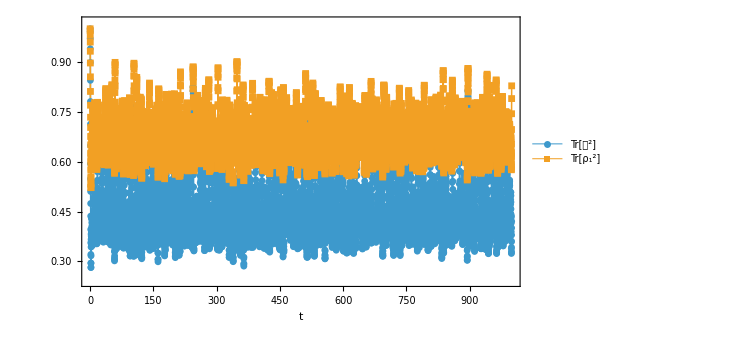
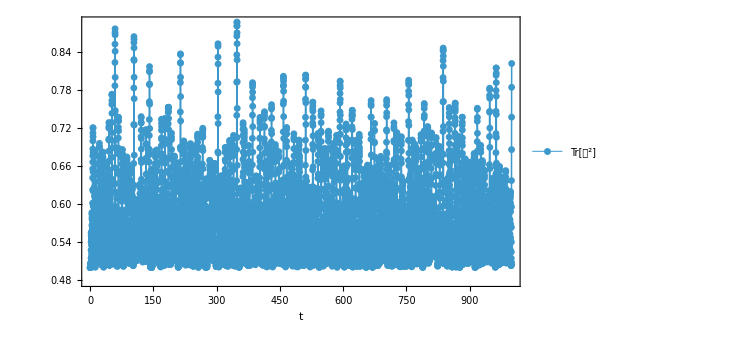

```mathematica
{fig1,fig2}
```

## (caotico) 0.5

```mathematica
L=3;
```

```mathematica
tf=1000.;
```

```mathematica
(*environment's initial state*)
ψ=RandomChainProductState[L-1];
```

```mathematica
(*parameters*) 

hx=1.;(*transverse field*)
hz=0.1;(*longitudinal field*)
J=1.;(*ising interaction*)
```

```mathematica
H=IsingHamiltonian[hx,hz,J,L];
{energies,eigenstates}=Eigensystem[Normal[H]];
```

```mathematica
state2design=Catenate[Eigenvectors[N@Pauli[#]]&/@Range[3]]
```

{{-0.707107,0.707107},{0.707107,0.707107},{0.-0.707107 ⅈ,-0.707107+0. ⅈ},{0.-0.707107 ⅈ,0.707107+0. ⅈ},{0.,-1.},{-1.,0.}}

```mathematica
purities=Table[
ℰ=Superoperator[t,ψ,energies,eigenstates,L];
{Purity[Reshuffle[ℰ]/2],Mean[Braket[#,#]&[ℰ.Flatten[Dyad[#]]]&/@state2design]}
,{t,0,tf,0.1}];
```

```mathematica
fig1=ListPlot[Transpose[{Range[0,tf,0.1],#}]&/@Transpose[purities],
PlotRange->{All,{0.24,1.02}},
Joined->True,
PlotMarkers->{Automatic,7},
PlotStyle->Directive[Thickness[0.002]],
PlotLegends->Placed[LineLegend[{TraditionalForm[Tr[𝒟^2]],TraditionalForm[Tr[Subscript[ρ, 1]^2]]},LabelStyle->Directive[Black,FontSize->22]], {Right,Top}],
Frame->True,
FrameStyle->Directive[Black,FontSize->25],
FrameLabel->{"t",""},
ImageSize->550
];
```

```mathematica
fig2=ListPlot[Transpose[{Range[0,tf,0.1],3/2*#2-#1&@@Transpose[purities]}],
PlotRange->{All,All},
Joined->True,
PlotMarkers->{Automatic,7},
PlotStyle->Directive[Thickness[0.002]],
PlotLegends->Placed[LineLegend[{TraditionalForm[Tr[𝒟^2]],TraditionalForm[Tr[Subscript[ρ, 1]^2]]},LabelStyle->Directive[Black,FontSize->22]], {Right,Top}],
Frame->True,
FrameStyle->Directive[Black,FontSize->25],
FrameLabel->{"t",""},
ImageSize->550
];
```

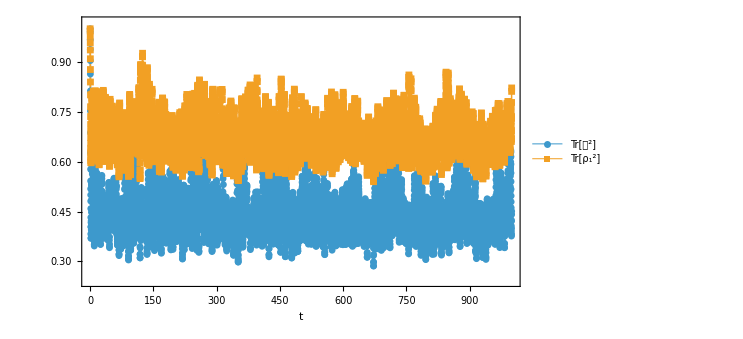
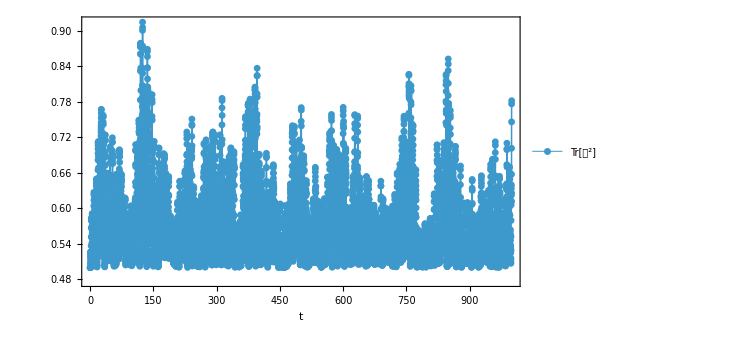

```mathematica
{fig1,fig2}
```

## (caotico) 0.5

```mathematica
L=3;
```

```mathematica
tf=1000.;
```

```mathematica
(*environment's initial state*)
ψ=RandomChainProductState[L-1];
```

```mathematica
(*parameters*) 

hx=1.;(*transverse field*)
hz=0.01;(*longitudinal field*)
J=1.;(*ising interaction*)
```

```mathematica
H=IsingHamiltonian[hx,hz,J,L];
{energies,eigenstates}=Eigensystem[Normal[H]];
```

```mathematica
state2design=Catenate[Eigenvectors[N@Pauli[#]]&/@Range[3]]
```

{{-0.707107,0.707107},{0.707107,0.707107},{0.-0.707107 ⅈ,-0.707107+0. ⅈ},{0.-0.707107 ⅈ,0.707107+0. ⅈ},{0.,-1.},{-1.,0.}}

```mathematica
purities=Table[
ℰ=Superoperator[t,ψ,energies,eigenstates,L];
{Purity[Reshuffle[ℰ]/2],Mean[Braket[#,#]&[ℰ.Flatten[Dyad[#]]]&/@state2design]}
,{t,0,tf,0.1}];
```

```mathematica
fig1=ListPlot[Transpose[{Range[0,tf,0.1],#}]&/@Transpose[purities],
PlotRange->{All,{0.24,1.02}},
Joined->True,
PlotMarkers->{Automatic,7},
PlotStyle->Directive[Thickness[0.002]],
PlotLegends->Placed[LineLegend[{TraditionalForm[Tr[𝒟^2]],TraditionalForm[Tr[Subscript[ρ, 1]^2]]},LabelStyle->Directive[Black,FontSize->22]], {Right,Top}],
Frame->True,
FrameStyle->Directive[Black,FontSize->25],
FrameLabel->{"t",""},
ImageSize->550
];
```

```mathematica
fig2=ListPlot[Transpose[{Range[0,tf,0.1],3/2*#2-#1&@@Transpose[purities]}],
PlotRange->{All,All},
Joined->True,
PlotMarkers->{Automatic,7},
PlotStyle->Directive[Thickness[0.002]],
PlotLegends->Placed[LineLegend[{TraditionalForm[Tr[𝒟^2]],TraditionalForm[Tr[Subscript[ρ, 1]^2]]},LabelStyle->Directive[Black,FontSize->22]], {Right,Top}],
Frame->True,
FrameStyle->Directive[Black,FontSize->25],
FrameLabel->{"t",""},
ImageSize->550
];
```

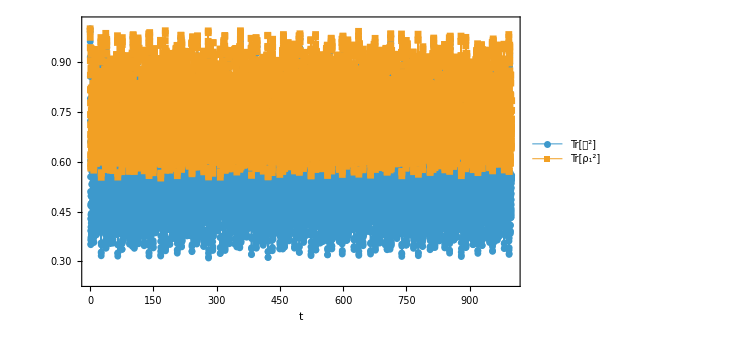
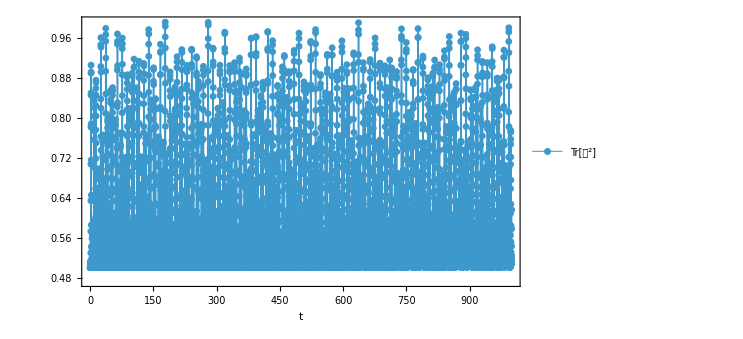

```mathematica
{fig1,fig2}
```